```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\PVP3_EG_Ag\100Ag\pmf_curve\100_windows_umbrella_sampling\11ns\k_0.7\101_window

```mathematica
log=OpenRead["thermo.lammps"]
```

InputStream[…]

```mathematica
Find[log,"# Step PotEng"];
```

```mathematica
thermo=ReadList[log,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
```

```mathematica
Close[log];
```

```mathematica
datafile=OpenRead["system.data"];
```

```mathematica
Find[datafile,"Description"]
```

LAMMPS Description

```mathematica
numbatom=Read[datafile,{Number,String}][[1]]
```

4688

```mathematica
Find[datafile,"impropers"];
```

```mathematica
numbatomtype=Read[datafile,{Number,String}][[1]]
```

16

```mathematica
Find[datafile,"Masses"]
```

Masses

```mathematica
masslist=ReadList[datafile,{Number,Number,String},numbatomtype][[All,2]]
```

{1.008,1.008,1.008,1.008,12.011,12.011,12.011,12.011,12.011,14.007,15.9994,1.008,1.008,12.011,15.9994,107.868}

```mathematica
Close[datafile];
```

```mathematica
trajfilename="traj_npt.lammpstrj"
```

traj_npt.lammpstrj

```mathematica
traj=OpenRead[trajfilename];
Find[traj,"TIMESTEP"]
```

ITEM: TIMESTEP

```mathematica
timestep=Read[traj,Number]
timesteptemp=timestep;
```

27620000

```mathematica
timeprod=2000;
timestepthermo=1000;
timesteptraj=20000;
(*Production time*)
```

```mathematica
(*Atoms per molecules, PVP = 90, 2PDO = 13, MB3 = 16, EPD = 19*)
(*DON'T FORGET TO MANUALLY EDIT EVERYTIME*)
sizepvp=10;
numbpvp=420;
```

```mathematica
firstpvpatomid=1;
lastpvpatomid=numbpvp*10;
```

```mathematica
lz=81.7009165297129;
```

```mathematica
(*pvpatomtypeseq={10,8,8,11,9,10,8,8,11,9};*)
```

```mathematica
pvpatomtypeseq={14,12,12,15,13,14,12,12,15,13};
```

```mathematica
masslist[[pvpatomtypeseq]]
```

{12.011,1.008,1.008,15.9994,1.008,12.011,1.008,1.008,15.9994,1.008}

```mathematica
masslistrep=Flatten[Table[masslist[[pvpatomtypeseq]],{i,numbpvp}]];
```

```mathematica
IfBelow[x_]:=If[x<0,1,0];
IfAbove[x_]:=If[x>lz,-1,0];
```

```mathematica
pvpposition=Reap[
While[!(timesteptemp===EndOfFile),
Find[traj,"ATOMS id mol type"];
atompositiontemp=Sort[ReadList[traj,{Number,Number,Number,Number,Number,Number, Number,Number,Number},numbatom]];
atompositiontemp[[All,1]]=timesteptemp;
pvppositiontemp=atompositiontemp[[1;;numbpvp*10]];
pvppositiontemp[[All,7]]=pvppositiontemp[[All,9]]*lz+pvppositiontemp[[All,6]];
pvpcomtemp=Total[Partition[pvppositiontemp[[All,7]]*masslistrep,sizepvp],{2}]/Total[masslist[[pvpatomtypeseq]]];
pvppositiontemp[[All,8]]=Flatten[Transpose[Table[pvpcomtemp+(IfBelow/@pvpcomtemp+IfAbove/@pvpcomtemp)*lz,{i,sizepvp}]]];
Sow[pvppositiontemp];
timestepdiff=timesteptemp-timesteptemp2;
timesteptemp2=timesteptemp;
Find[traj,"TIMESTEP"];
timesteptemp = Read[traj,Number];
]
][[2,1]];//AbsoluteTiming
```

{4.02023,Null}

```mathematica
timesteptemp2
```

29600000

```mathematica
pvpposition=Partition[Flatten[pvpposition],9]
```

{{27620000,1,14,8.76232,9.28935,25.9361,25.9361,25.9838,0},{27620000,1,12,9.58339,8.9457,26.6371,26.6371,25.9838,0},{27620000,1,12,8.63488,8.57607,25.081,25.081,25.9838,0},419994,{29600000,420,12,11.4937,21.6892,29.0952,110.796,29.849,1},{29600000,420,15,11.6424,23.5446,30.0052,111.706,29.849,1},{29600000,420,13,11.9024,23.1362,30.8508,112.552,29.849,1}}
 |  |  |  |

```mathematica
(* pvpposition *)
(* Layer 1: Individual atoms at each timestep *)
(* {timestep, atomid, atomtype, x, y, z, nonperiodic-z, com-z, periodicbox-z} *)
```

```mathematica
Close[traj];
```

```mathematica
(*Density profile*)
```

```mathematica
pvpcom=Partition[pvpposition[[1;;-1;;sizepvp,8]],numbpvp];
```

```mathematica
(* pvpcom *)
(* com-z of each pvp molecules at each timestep *)
(* arranged in order of pvp1timestep1, ..., pvp18timestep1, pvp1timestep2, ..., pvp18timestep2, ..., pvp18timestepend *)
```

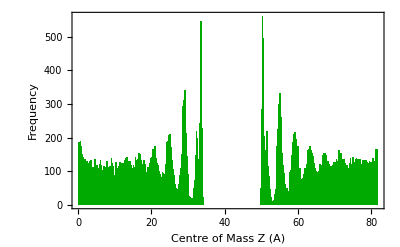

```mathematica
ComzHist=Histogram[Flatten[pvpcom],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
LowerBot=Input["Lower of bottom layer",32]
```

32

```mathematica
UpperBot=Input["Upper of bottom layer",40]
```

40

```mathematica
BottomLayerCount=Flatten[Reap[For[i=1,i≤Length[pvpcom],i++,
Sow[BinCounts[pvpcom[[i]],{{LowerBot,UpperBot}}]];
];][[2,1]]];
```

```mathematica
N[Mean[BottomLayerCount]]
```

24.4

```mathematica
CreateDirectory["density"];
```

```mathematica
Export["density/Histogram.png",ComzHist,ImageResolution->300];
```

```mathematica
Export["density/report.txt",{"Mean Bottom Layer Count:",N[Mean[BottomLayerCount]]," ","Lower of bottom layer:",LowerBot," ","Upper of bottom layer:",UpperBot}]
```

density/report.txt